#### 3.2Gompertz Equation with Continuous Injection Coupled with Logistic Equation

```mathematica
Quit[]
```

```mathematica
sol = DSolve[{p'[t]==-α*p[t]*Log[p[t]/((q0*k)/(q0+(k-q0)*Exp[-β*t]))]-u*p[t],p[0]==p0},p[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→1/(k-q0+ⅇ^(t β) q0)ⅇ^(-u/α+t β-(β Hypergeometric2F1[1,α/β,1+α/β,-(ⅇ^(t β) q0)/(k-q0)])/α-(ⅇ^(-t α) k (-u-β Hypergeometric2F1[1,α/β,1+α/β,-q0/(k-q0)]-α Log[p0/q0]))/((k-q0) α)+(ⅇ^(-t α) q0 (-u-β Hypergeometric2F1[1,α/β,1+α/β,-q0/(k-q0)]-α Log[p0/q0]))/((k-q0) α)) k q0}}

```mathematica
sol1 = Simplify[sol]
```

{{p[t]→1/(k+(-1+ⅇ^(t β)) q0)ⅇ^((ⅇ^(-t α) (u-ⅇ^(t α) u+ⅇ^(t α) t α β+β Hypergeometric2F1[1,α/β,(α+β)/β,-q0/(k-q0)]-ⅇ^(t α) β Hypergeometric2F1[1,α/β,(α+β)/β,-(ⅇ^(t β) q0)/(k-q0)]+α Log[p0/q0]))/α) k q0}}

```mathematica
q0=5;p0=3;k=9;α=2;β=8;u=1;
```

```mathematica
p31[t_]:=Evaluate[p[t]/.sol1]
```

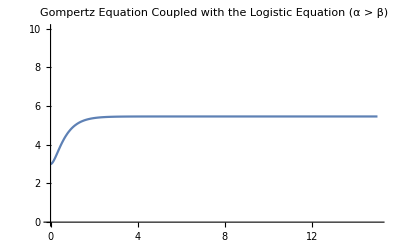

```mathematica
Plot[p31[t],{t,0,15},PlotRange->{0,10},PlotLabel->"Gompertz Equation Coupled with the Logistic Equation (α > β)"]
```